# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\enviroment state dependence

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

# XXZ Chain

## Hamiltonian

```mathematica
L=9;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

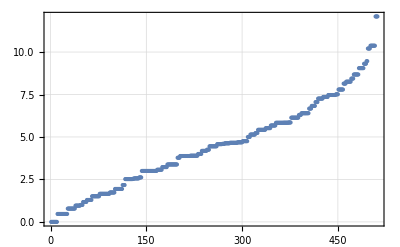

```mathematica
ListPlot[eigenval,PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
iprs=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

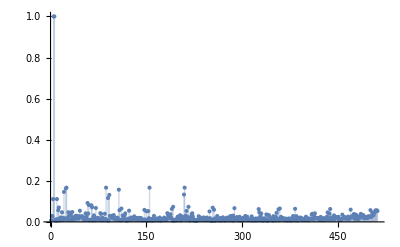

```mathematica
ListPlot[iprs,PlotRange->All,Filling->Axis]
```

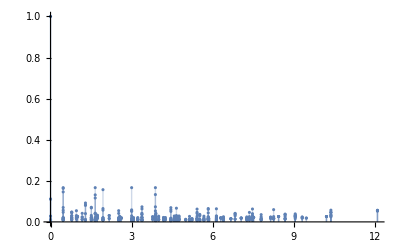

```mathematica
ListPlot[Transpose[{eigenval,iprs}],PlotRange->All,Filling->Axis]
```

## SP(t)

```mathematica
L=5;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=2;
caometer=Table[haar[1],{i,ale}];
ψTc=RandomChainProductState[L-1];
```

```mathematica
ψc=ParallelTable[Flatten[KroneckerProduct[i,ψTc]],{i,caometer}];
```

```mathematica
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
```

```mathematica
tf=10.0;
tlist=Range[0,tf,0.1];
ψct=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψc},{t,0,tf,0.1}];
```

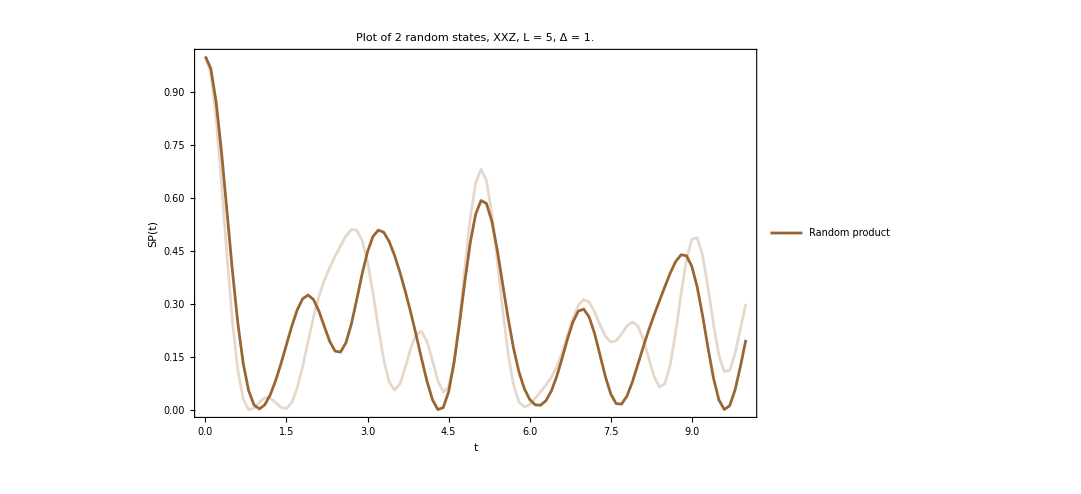

```mathematica
singlec=ListPlot[Table[{tlist[[i]],Abs[Conjugate[ψct[[j,1]]].ψct[[j,i]]]^2},{j,Length[ψct]},{i,Length[Range[0,tf,0.1]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Brown],Directive[Brown,Opacity[0.25]]},PlotRange->All,ImageSize->800,PlotLegends->{Style["Random product",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
densityc=Table[Dyad[i,i],{i,ψct}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
traceDistance[rho_,sigma_]:=1/2*Tr[MatrixPower[ConjugateTranspose[rho-sigma].(rho-sigma),1/2]];
```

```mathematica
tracedis=Table[traceDistance[i,Dyad[caometer[[1]]]],{i,reducedc}];
```

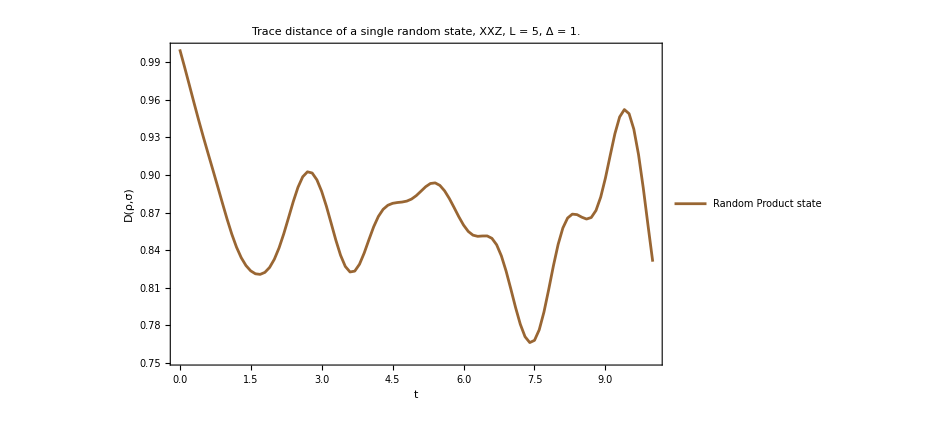

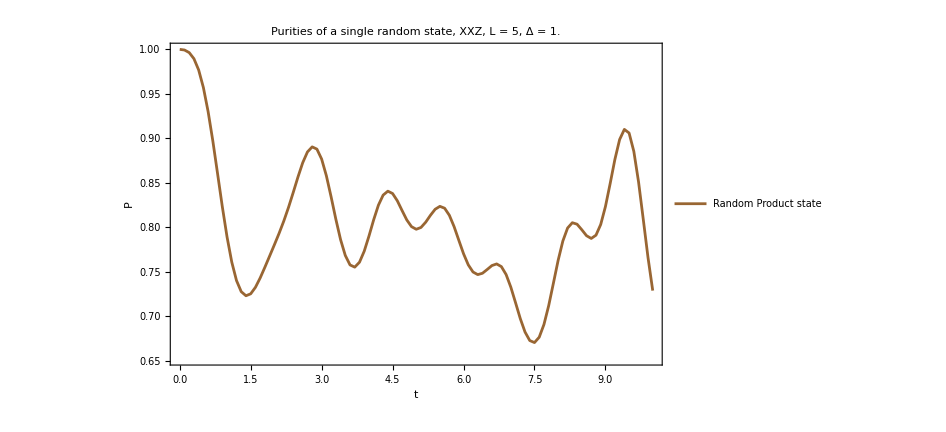

```mathematica
ListPlot[Transpose[{tlist,1-tracedis}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Trace distance of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["D(ρ,σ)"]}]

ListPlot[Transpose[{tlist,puritiesc}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

```mathematica
reducedmagcx=Table[Chop[Tr[sx.i]],{i,reducedc}];
reducedmagcy=Table[Chop[Tr[sy.i]],{i,reducedc}];
reducedmagcz=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

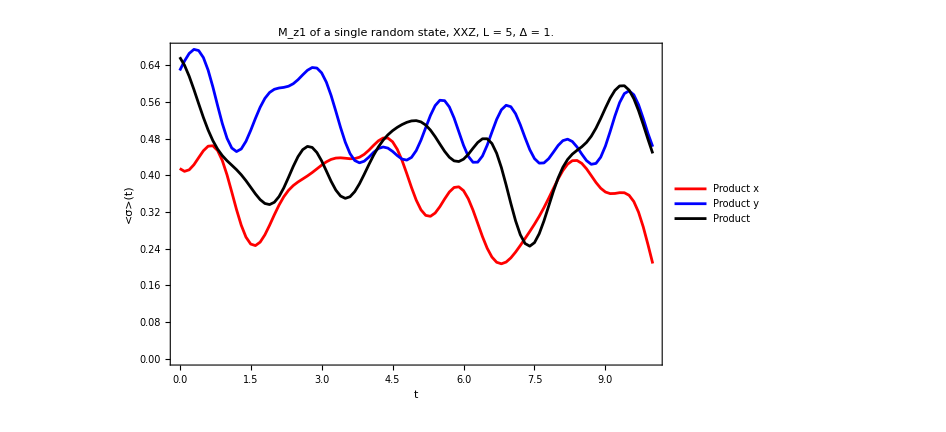

```mathematica
ListPlot[{Transpose[{tlist,reducedmagcx}],Transpose[{tlist,reducedmagcy}],Transpose[{tlist,reducedmagcz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Blue,Black},PlotRange->All,ImageSize->700,PlotLegends->{Style["Product x",Red],Style["Product y",Blue],Style["Product ",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]}]
```

# Quantum channel

## Sweep XXZ various chaometer states (only random product state)

```mathematica
L=5;
(*ψe=RandomChainProductState[L-1];*)
(*ψe=coherentstate[qubit[Pi,0],L-1];*)
(*ψe=Table[coherentstate[i,L-1],{i,caometer}];*)
```

```mathematica
tf=10.;
limit=Plot[0.25,{x,0,50.},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
ale=10;
caometer=Table[haar[1],{i,ale}];
```

```mathematica
Δ=1;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
hx=J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ψe=Table[haar[L-1],{i,caometer}];
```

```mathematica
ψe=Table[Flatten[KroneckerProduct[haar[1],coherentstate[qubit[0,0],L-2]]],{i,caometer}];
```

```mathematica
(*QUANTUM CHANNEL*)
(*styles={Style["Random product state, L = "<>ToString[L]<>", Δ = "<>ToString[Δ],40,Black]};*)
styles={Style["Coherent state random, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
   figs={};
listplots={};
purities={};
directionsx={};
directionsy={};
directionsz={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
choidirectionsx={};
choidirectionsy={};
choidirectionsz={};

Do[
superOp=Superoperator[t,ψe[[i]],eigenval,eigenvec,L];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];
,{t,0,tf,.1}];

AppendTo[listplots,
Show[{
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]
,limit}]];

AppendTo[purities,Show[{
ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]
,limit}]];
,{i,1}];
```

```mathematica
allpurities={};
Do[

(*REDUCED DYNAMICS*)
(*ψc=Flatten[KroneckerProduct[caometer[[i]],ψe]];*)
ψc=coherentstate[caometer[[i]],L];
ψct=Table[StateEvolution[t,ψc,eigenval,eigenvec],{t,0,tf,0.1}];
densityc=Table[Dyad[i,i],{i,ψct}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesc=Table[Chop[Purity[i]],{i,reducedc}];
AppendTo[allpurities,puritiesc];
,{i,Length[caometer]}];
```

$Aborted

```mathematica
tlist=Range[0,tf,0.1];
puritiesplot=ListPlot[Table[Transpose[{tlist,Chop[i]}],{i,allpurities}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->Directive[Brown,Opacity[0.05]],PlotRange->All,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]},ImageSize->950];
puritymeanplot=ListPlot[Transpose[{tlist,Mean[allpurities]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->Directive[Brown,Opacity[1]],PlotRange->All,PlotLegends->{Style["Random Product state",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]},ImageSize->950];
purityplot=Show[{puritymeanplot,puritiesplot},PlotRange->{All,{0.48,1.01}}];
```

```mathematica
testimage=Grid[{{listplots,purities,purityplot}},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
(*Export["testframe_coherent0_XXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>"_caometer.png",testimage];*)
Export["testframe_wisniacki_coherent_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_caometer.png",testimage];
```

```mathematica
testimage=Grid[{listplots,purities},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
(*Export["testframe_coherent0_XXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>"_caometer.png",testimage];*)
Export["testframe_wisniacki_haar_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_caometer.png",testimage];
```

## Spectrum ϵ

```mathematica
L=5;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
L=5;
hx=J=1.;
hz=4.;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
(*ψe=Table[RandomChainProductState[L-1],{i,caometer}];*)
ψe=RandomChainProductState[L-1];
```

```mathematica
tf=100.;
data1={};
data2={};
data3={};
Do[
superOp=Superoperator[t,ψe,eigenval,eigenvec,L];
(*AppendTo[choiEigenvalues,Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];*)
AppendTo[data1,Transpose[Sort[Transpose[Eigensystem[superOp]]]]];
,{t,0,tf,0.1}];
```

```mathematica
eigenvalues=Table[data1[[i,1]],{i,Length[data1]}];
eigenvectors=Table[data1[[i,2]],{i,Length[data1]}];
```

```mathematica
Export["spectrums_regular.png",Show[{uno,dos,tres,cuatro}]]
```

spectrums_regular.png

```mathematica
cuatro=ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->600,PlotTheme->"Detailed",PlotStyle->Gray,PlotLabel->Style["Wisniacki hz ="<>ToString[hz]<>", tf = "<>ToString[tf],25,Black]];
```

```mathematica
tres=ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->600,PlotTheme->"Detailed",PlotStyle->Brown,PlotLabel->Style["Wisniacki hz ="<>ToString[hz]<>", tf = "<>ToString[tf],25,Black]];
```

```mathematica
dos=ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->600,PlotTheme->"Detailed",PlotStyle->Red,PlotLabel->Style["Wisniacki hz ="<>ToString[hz]<>", tf = "<>ToString[tf],25,Black]];
```

```mathematica
uno=ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->600,PlotTheme->"Detailed",PlotStyle->Blue,PlotLabel->Style["Wisniacki hz ="<>ToString[hz]<>", tf = "<>ToString[tf],25,Black]];
```

```mathematica
plots=Table[ComplexListPlot[eigenvalues[[1;;i]],PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Gray],{i,1,50}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

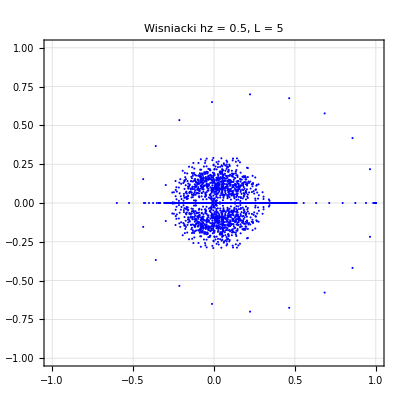

```mathematica
ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Blue,PlotLabel->Style["Wisniacki hz = "<>ToString[hz]<>", L = 5",25,Black]]
```

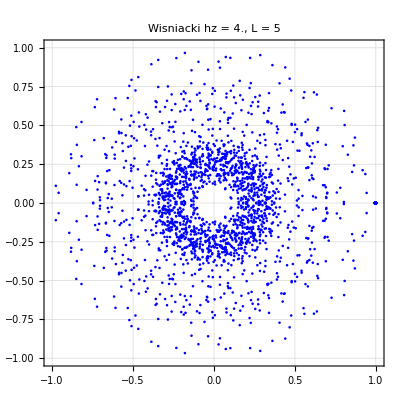

```mathematica
ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Blue,PlotLabel->Style["Wisniacki hz = "<>ToString[hz]<>", L = 5",25,Black]]
```

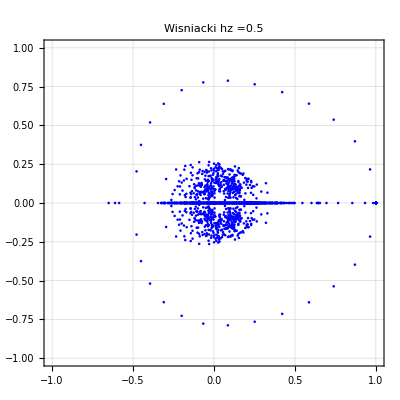

```mathematica
ComplexListPlot[eigenvalues,PlotRange->{{-1.01,1.01},{-1.01,1.01}},AspectRatio->1,ImageSize->400,PlotTheme->"Detailed",PlotStyle->Blue,PlotLabel->Style["Wisniacki hz ="<>ToString[hz],25,Black]]
```

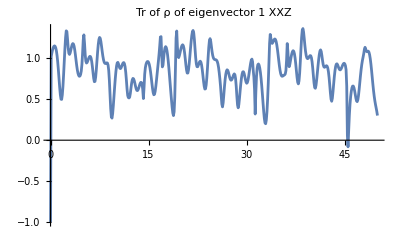

```mathematica
ρcheck=Table[Tr[bloch[rho[eigenvectors[[i,4]]]]],{i,Length[data1]}];
ListPlot[Transpose[{Range[0,50,0.1],Chop[ρcheck]}],PlotLabel->Style["Tr of ρ of eigenvector 1 XXZ", Black,18],PlotRange->All,Joined->True]
```

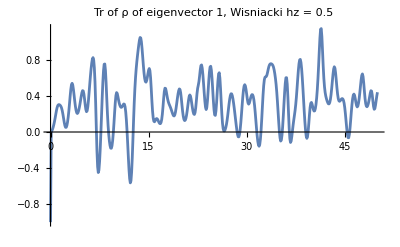

```mathematica
ρcheck=Table[Tr[bloch[rho[eigenvectors[[i,4]]]]],{i,Length[data1]}];
ListPlot[Transpose[{Range[0,50,0.1],Chop[ρcheck]}],PlotLabel->Style["Tr of ρ of eigenvector 1, Wisniacki hz = "<>ToString[hz], Black,18],PlotRange->All,Joined->True]
```

## Average over coherent states ψe

```mathematica
L=6;
tf=20.;
limit=Plot[0.25,{x,0,50.},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
ale=50;
caometer=Table[haar[1],{i,ale}];
(*ψe=Table[coherentstate[i,L-1],{i,caometer}];*)
(*ψe=Table[RandomChainProductState[L-1],{i,ale}];*)
(*ψe=Table[haar[L-1],{i,caometer}];*)
```

```mathematica
Δ=1;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
hx=J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=100;
caometer=Table[haar[1],{i,ale}];
ψTa=Table[haar[L-1],{i,ale}];
ψTc=Table[RandomChainProductState[L-1],{i,ale}];
```

```mathematica
ψa=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTa},{i,caometer}],{ale*ale,2^L}];
ψc=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTc},{i,caometer}],{ale*ale,2^L}];
```

```mathematica
energiesa=ParallelTable[Chop[Conjugate[i].H.i],{i,ψa}];
energiesc=ParallelTable[Chop[Conjugate[i].H.i],{i,ψc}];
```

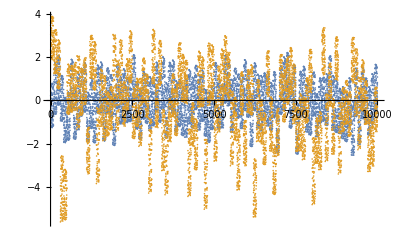

```mathematica
ListPlot[{energiesa,energiesc},PlotRange->All]
```

```mathematica
(*Find positions of elements within the range-2 to 2*)
positionsa=Position[energiesa,x_/;-2<=x<=2];
positionsc=Position[energiesc,x_/;-2<=x<=2];
```

```mathematica
ψea=Table[ψTa[[i]],{i,Flatten[positionsa]}];
ψec=Table[ψTc[[i]],{i,Flatten[positionsc]}];
```

Part::partw: Part 101 of {{0.143194+0.131395 ⅈ,-0.1679-0.049073 ⅈ,0.0490768+0.205951 ⅈ,-0.0616339-0.0514467 ⅈ,0.0182257-0.061388 ⅈ,-0.127954+0.21868 ⅈ,«21»,-0.203705+0.0263231 ⅈ,0.1919-0.0842438 ⅈ,-0.053459-0.0562309 ⅈ,0.0787842-0.0655159 ⅈ,0.00881744+0.0000331985 ⅈ},{«1»},{«1»},«46»,{«1»},«50»} does not exist.

Part::partw: Part 102 of {{0.143194+0.131395 ⅈ,-0.1679-0.049073 ⅈ,0.0490768+0.205951 ⅈ,-0.0616339-0.0514467 ⅈ,0.0182257-0.061388 ⅈ,-0.127954+0.21868 ⅈ,«21»,-0.203705+0.0263231 ⅈ,0.1919-0.0842438 ⅈ,-0.053459-0.0562309 ⅈ,0.0787842-0.0655159 ⅈ,0.00881744+0.0000331985 ⅈ},{«1»},{«1»},«46»,{«1»},«50»} does not exist.

Part::partw: Part 103 of {{0.143194+0.131395 ⅈ,-0.1679-0.049073 ⅈ,0.0490768+0.205951 ⅈ,-0.0616339-0.0514467 ⅈ,0.0182257-0.061388 ⅈ,-0.127954+0.21868 ⅈ,«21»,-0.203705+0.0263231 ⅈ,0.1919-0.0842438 ⅈ,-0.053459-0.0562309 ⅈ,0.0787842-0.0655159 ⅈ,0.00881744+0.0000331985 ⅈ},{«1»},{«1»},«46»,{«1»},«50»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 102 of {«1»} does not exist.

Part::partw: Part 105 of {«1»} does not exist.

Part::partw: Part 106 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ψea//Length
ψec//Length
```

9861

7450

```mathematica
ψe=ψTc[[1;;-1;;100]];
```

```mathematica
ψe//Length
```

75

```mathematica
(*QUANTUM CHANNEL*)
styles={Style["Coherent state random, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
allchoieigenvalues={};
allchoipurities={};

Do[

choiEigenvalues={};
choipurities={};

Do[
superOp=Superoperator[t,ψe[[i]],eigenval,eigenvec,L];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];
,{t,0,tf,.1}];

AppendTo[allchoieigenvalues,
Chop[choiEigenvalues]];
AppendTo[allchoipurities,Chop[choipurities]];
,{i,Length[ψe]}];
```

```mathematica
listplots={};
puritiesplots={};

Do[

AppendTo[listplots,
Show[{
ListPlot[Transpose[Chop[allchoieigenvalues[[i]]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Opacity[0.15]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

AppendTo[puritiesplots,
Show[{
ListPlot[Chop[allchoipurities[[i]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Gray,Opacity[0.15]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

,{i,Length[ψe]}];
```

```mathematica
plotmeanchoieigenval=ListPlot[Transpose[Chop[Mean[allchoieigenvalues]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];

plotmeanchoipurity=ListPlot[Chop[Mean[allchoipurities]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Black,Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];
```

```mathematica
testimage=Grid[{{Show[{plotmeanchoieigenval,listplots}]},{Show[{plotmeanchoipurity,puritiesplots},PlotRange->{{0,20},All}]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
(*Export["testframe_coherent_XXZ_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>"_caometer.png",testimage];*)
Export["testframe_wisniacki_haar_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_caometer.png",testimage];
```

```mathematica
Show[{plotmeanchoieigenval,listplots}];
Show[{plotmeanchoipurity,puritiesplots}];
```